```mathematica
dir=NotebookDirectory[]
```

/home/nicolas/git/spectrum_quasicrystals/Fibonacci/

```mathematica
(* Thickness *)
th=0.003;
```

## Setup and tests

### Hamiltonians

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with periodic bc *)
hp[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,1,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with antiperiodic bc *)
ha[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,2,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
PrependTo[tblw,{1,1+F0}->-tw];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
ha[4,tw,ts]//MatrixForm
```

(0 | 0 | 0 | -tw | 0 | ts | 0 | 0
0 | 0 | 0 | 0 | tw | 0 | ts | 0
0 | 0 | 0 | 0 | 0 | tw | 0 | ts
-tw | 0 | 0 | 0 | 0 | 0 | tw | 0
0 | tw | 0 | 0 | 0 | 0 | 0 | tw
ts | 0 | tw | 0 | 0 | 0 | 0 | 0
0 | ts | 0 | tw | 0 | 0 | 0 | 0
0 | 0 | ts | 0 | tw | 0 | 0 | 0)

```mathematica
(* wavefunctions in the co-basis, ordered by IDoS label *)
wf=Block[{val,vec,i=9,ts=10.,tw=1.},
{val,vec}=Eigensystem[hp[i,tw,ts]];
(*order wavefunctions by increasing energy*)
vec[[Ordering[val]]]
];
```

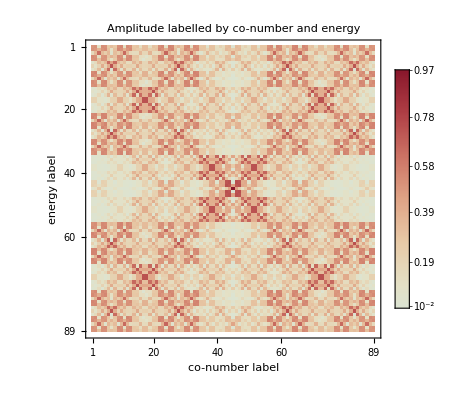

```mathematica
MatrixPlot [Abs[wf],FrameLabel->{"energy label","co-number label"},PlotLabel->"Amplitude labelled by co-number and energy",PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
```

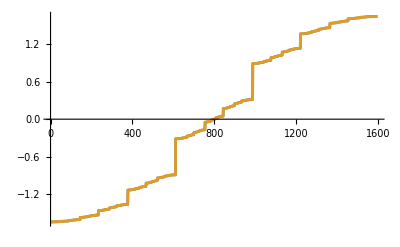

```mathematica
Block[{ts=.5,tw=1.,vpp,vpa,i=15},
vpp=Sort@Eigenvalues[hp[i,tw,ts]];
vpa=Sort@Eigenvalues[ha[i,tw,ts]];
ListPlot[{vpp,vpa},Joined->True,PlotStyle->Thickness[0.005]]
]
```

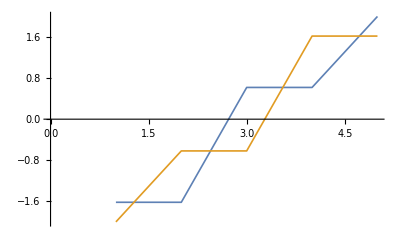

```mathematica
Block[{mp,ma,vpp,vpa,i=3},
mp=Table[DiscreteDelta[j-k+1]+DiscreteDelta[j-k+Fibonacci[i+2]-1],{j,Fibonacci[i+2]},{k,Fibonacci[i+2]}];
mp=mp+Transpose@mp;
ma=Table[DiscreteDelta[j-k+1]-DiscreteDelta[j-k+Fibonacci[i+2]-1],{j,Fibonacci[i+2]},{k,Fibonacci[i+2]}];
ma=ma+Transpose@ma;
vpp=Sort[Eigenvalues[mp]//N];
vpa=Sort[Eigenvalues[ma]//N];
ListPlot[{vpp,vpa},Joined->True,PlotStyle->Thickness[th]]
]
```

### Partition function

#### Definitions

Note that the effective bands are the largest when tw = ts. In that case and for q ≤ 1 all fractal dimensions should be equal to 1 (and therefore τ(q ≤ 1) = q-1), whereas for we should have τ(q ⟩ 1) = q/2. Numerically, the convergence using our effective bandwidths is very slow, and the larger q gets, the slower the convergence is. This is probably because the bands are so large in that case. 
I do hope that the smaller tw/ts is, the faster the convergence will be!

```mathematica
(* Compute the fractal dimension Subscript[D, q0] for a system of size fib(i+2) *)
Clear[FractalD];
FractalD[i_,tw_,ts_,q0_]:=Block[{vpp,vpa,vppN,vpaN,bandlist,bandlistN,gam,gamN,τ0},
(* spectres des systèmes de taille i p et anti-p *)
vpp=Sort[Eigenvalues[hp[i,tw,ts]]];
vpa=Sort[Eigenvalues[ha[i,tw,ts]]];
(* spectres des systèmes de taille i+1 p et anti-p *)
vppN=Sort[Eigenvalues[hp[i+1,tw,ts]]];
vpaN=Sort[Eigenvalues[ha[i+1,tw,ts]]];
(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bandlist=MapThread[Abs[#1-#2]&,{vpa,vpp}];
bandlistN=MapThread[Abs[#1-#2]&,{vpaN,vppN}];
(* calcul des fonctions de partition Subscript[Γ, i] et Subscript[Γ, i+1] *)
gam=Fibonacci[i+2]^-q Plus@@((bandlist)^-τ);
gamN=Fibonacci[i+3]^-q Plus@@((bandlistN)^-τ);
(* Subscript[D, q0] *)
τ0=τ/.FindRoot[(gamN/gam/.q->q0)-1,{τ,0}];
τ0
]
```

On a τ(q > 1) =q/2 et τ(q ≤ 1) = q-1 quand t_w=t_s. → singularités de van Hove !

```mathematica
FractalD[13,1.,1.,20]
```

10.

Because Γ^(n+1)/Γ^n=ω^q((Σ(Δ^(n+1)))^(-τ(q)))/((Σ(Δ^n))^(-τ(q)))=1 it is hard to compute τ(q) but easy to get q(τ).
We have
q(τ) = (B^n(τ)-B^(n+1)(τ))/(Log(q))
where
B^n(τ)=Log[(Σ(Δ^n))^-τ]

Next, we want to compute f-α. Easy!
α(τ)=(q'(τ))^-1
and
f(α(τ)) = q(τ)α(τ) - τ

For q<0, it seems to converge way better if we compute Γ^(n+2)/Γ^n rather than Γ^(n+1)/Γ^n. Why?

```mathematica
(* Return banlists *)
BandLists[i_,tw_,ts_]:=Block[{vpp,vpa,vppN,vpaN,bandlist,bandlistN},
(* spectres des systèmes de taille i p et anti-p *)
vpp=Sort[Eigenvalues[hp[i,tw,ts]]];
vpa=Sort[Eigenvalues[ha[i,tw,ts]]];
(* spectres des systèmes de taille i+1 p et anti-p *)
vppN=Sort[Eigenvalues[hp[i+1,tw,ts]]];
vpaN=Sort[Eigenvalues[ha[i+1,tw,ts]]];
(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bandlist=MapThread[Abs[#1-#2]&,{vpa,vpp}];
bandlistN=MapThread[Abs[#1-#2]&,{vpaN,vppN}];
{bandlist,bandlistN}
]
```

```mathematica
(* Plot τ -> {α(τ),f(α(τ))} *)
Clear[FractalFa];
FractalFa[τmin_,τmax_,bandlist_,bandlistN_]:=Block[{q,alpha,f,om=N[2/(1+√5)]},
(* q(τ) *)
q=Log[Plus@@((bandlist)^-τ)/Plus@@((bandlistN)^-τ)]/Log[om];
(*Print[ParametricPlot[{q,τ},{τ,-10,10},AxesLabel->{"q","τ(q)"}]];*)
alpha=1./D[q,τ];
ParametricPlot[{alpha,alpha q-τ},{τ,τmin,τmax},AspectRatio->1,PlotRange->All,AxesLabel->{"α","f(α)"}]
]
```

In the ρ = 1 case, we find two possible values for α:
α(q > 1) = 1/2
α(q ≤ 1) = 1
and for f:
f(1/2) = 0
f(1) = 1

If we compute numerically the Legendre transform of τ for a finite size system, we find a continuum of values of α ranging from 1/2 to 1.
We check that indeed f(1/2) = 0, f(1) = 1.

```mathematica
{b,bnew}=BandLists[14,1.,1.];
```

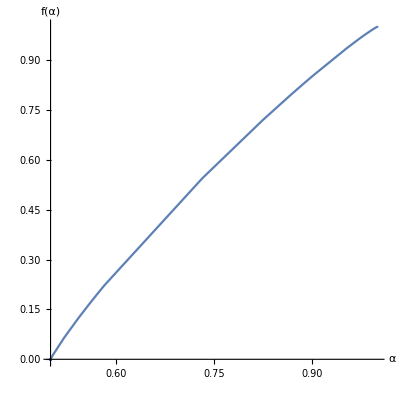

```mathematica
p=FractalFa[-2,50,b,bnew]
```

```mathematica
{b,bnew}=BandLists[14,.1,1.];
```

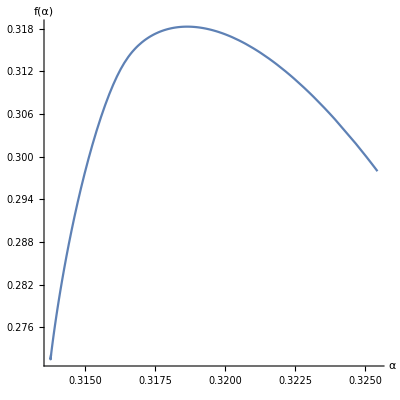

```mathematica
p=FractalFa[-2,12,b,bnew]
```

In the framework of the asymptotic formulas, if ρ < 1/8, α is an increasing function of the parameter x, while it is decreasing in the other case. 
So it seems that the validity of the asymptotic formulas is ρ < 1/8.

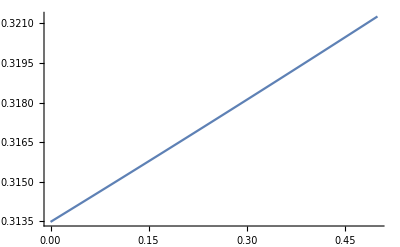

```mathematica
ρ=1/10;
om=N[2/(1+√5)];
z=ρ/2;barz=ρ^2;
α[x_]:=Log[om]/(x Log[z]+(1-2x)/3Log[barz]);
Plot[α[x],{x,0,1/2}]
```

#### Tests

```mathematica
(* asymptotically exact solution in the ρ->0 limit *)
exactFD[ρ_,q_]:=Block[{ω=1/GoldenRatio,z,barz},
z=ρ/2;
barz=ρ^2;
τ/.FindRoot[2 ω^(2q)z^-τ+ω^(3q)barz^-τ-1,{τ,10}]
]
```

```mathematica
start=2;
stop=16;
d0=ParallelTable[FractalD[i,1/10.,1.,0],{i,start,stop}]
```

Système de taille fib(n), n = 4

Système de taille fib(n), n = 6

Système de taille fib(n), n = 8

Système de taille fib(n), n = 10

Système de taille fib(n), n = 5

Système de taille fib(n), n = 7

Système de taille fib(n), n = 9

Système de taille fib(n), n = 11

Système de taille fib(n), n = 12

Système de taille fib(n), n = 13

Système de taille fib(n), n = 14

Système de taille fib(n), n = 15

Système de taille fib(n), n = 16

Système de taille fib(n), n = 17

Système de taille fib(n), n = 18

{-0.468077,-0.26209,-0.367179,-0.292778,-0.336534,-0.306884,-0.325309,-0.313124,-0.320869,-0.315809,-0.319057,-0.316947,-0.318307,-0.317426,-0.317995}

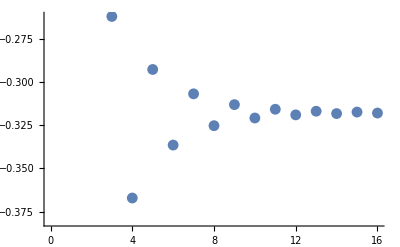

-0.314387

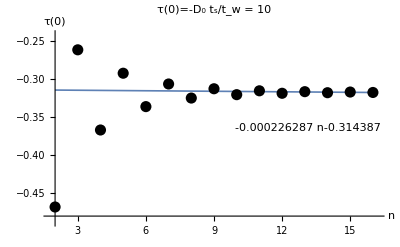

```mathematica
Block[{fit,data,plot},
data=MapThread[{#1,#2}&,{Range[start,stop],d0}];
Print[ListPlot[data]];
fit=LinearModelFit[data[[start+10;;]],n,n];
Print[Normal[fit]/.n->0];
plot=Plot[Normal@fit,{n,start,stop},PlotRange->{{start-0.2,stop+0.2},{Min[d0]-0.02,Max[d0]+0.02}},Epilog->{PointSize@.02,Point@data},AxesLabel->{"n","τ(0)"},PlotLabel->"τ(0)=-D_0 \n t_s/t_w = 10",PlotStyle->Thickness[th],PlotLegends->Placed[Normal@fit,{Right,Center}]];
Print[plot];
(*Export[dir<>"/data/hausdorff.pdf",plot];*)
]
```

```mathematica
start=2;
stop=16;
d2=ParallelTable[FractalD[i,1/2.,1.,2],{i,start,stop}]
```

Système de taille fib(n), n = 4

Système de taille fib(n), n = 6

Système de taille fib(n), n = 8

Système de taille fib(n), n = 10

Système de taille fib(n), n = 5

Système de taille fib(n), n = 7

Système de taille fib(n), n = 9

Système de taille fib(n), n = 11

Système de taille fib(n), n = 12

Système de taille fib(n), n = 13

Système de taille fib(n), n = 14

Système de taille fib(n), n = 15

Système de taille fib(n), n = 16

Système de taille fib(n), n = 17

Système de taille fib(n), n = 18

{0.72461,0.605398,0.679505,0.631598,0.664941,0.640894,0.658364,0.645304,0.654958,0.647685,0.653101,0.649019,0.652069,0.649773,0.651492}

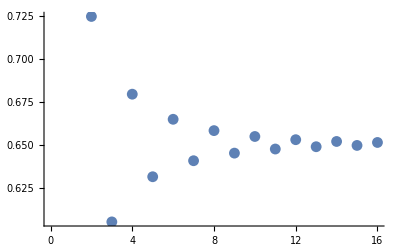

0.655441

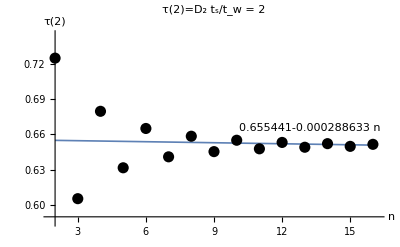

```mathematica
Block[{fit,data,plot},
data=MapThread[{#1,#2}&,{Range[start,stop],d2}];
Print[ListPlot[data]];
fit=LinearModelFit[data[[start+11;;]],n,n];
Print[Normal[fit]/.n->0];
plot=Plot[Normal@fit,{n,start,stop},PlotRange->{{start-0.2,stop+0.2},{Min[d2]-0.02,Max[d2]+0.02}},Epilog->{PointSize@.02,Point@data},AxesLabel->{"n","τ(2)"},PlotLabel->"τ(2)=D_2 \n t_s/t_w = 2",PlotStyle->Thickness[th],PlotLegends->Placed[Normal@fit,{Right,Center}]];
Print[plot];
(*Export[dir<>"/data/renyi_entropy_2.pdf",plot];*)
]
```

```mathematica
start=2;
stop=16;
d20=ParallelTable[FractalD[i,1/2.,1.,20],{i,start,stop}]
```

Système de taille fib(n), n = 4

Système de taille fib(n), n = 6

Système de taille fib(n), n = 8

Système de taille fib(n), n = 10

Système de taille fib(n), n = 5

Système de taille fib(n), n = 7

Système de taille fib(n), n = 9

Système de taille fib(n), n = 11

Système de taille fib(n), n = 12

Système de taille fib(n), n = 13

Système de taille fib(n), n = 14

Système de taille fib(n), n = 15

Système de taille fib(n), n = 16

Système de taille fib(n), n = 17

Système de taille fib(n), n = 18

{11.208,8.64141,10.3762,8.72053,10.2621,8.7331,10.2458,8.73509,10.2434,8.7354,10.2431,8.73545,10.243,8.73546,10.243}

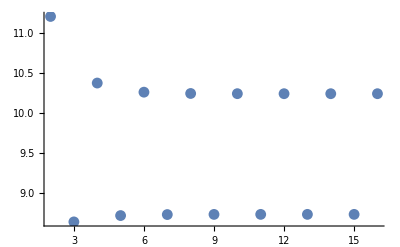

10.24728.73466

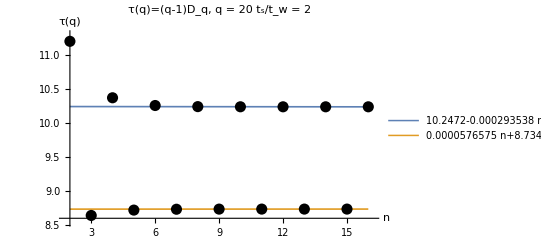

```mathematica
Block[{fit,data,plot},
data=MapThread[{#1,#2}&,{Range[start,stop],d20}];
Print[ListPlot[data,PlotRange->All]];
fitSup=LinearModelFit[data[[start+5;;;;2]],n,n];
fitInf=LinearModelFit[data[[start+6;;;;2]],n,n];
Print[Normal[fitSup]/.n->0,Normal[fitInf]/.n->0];
plot=Plot[{Normal@fitSup,Normal@fitInf},{n,start,stop},PlotRange->{{start-0.2,stop+0.2},{Min[d20]-0.1,Max[d20]+0.1}},Epilog->{PointSize@.02,Point@data},AxesLabel->{"n","τ(q)"},PlotLabel->"τ(q)=(q-1)D_q, q = 20 \n t_s/t_w = 2",PlotStyle->Thickness[th],PlotLegends->Placed[{Normal@fitSup,Normal@fitInf},{Right,Center}]];
Print[plot];
Export[dir<>"/data/renyi_q20_2.pdf",plot];
]
```

#### Comparison partition function/box counting

Return the spectrum rescaled to fit into the [0,1] interval

```mathematica
spect[i_,tw_,ts_]:=Block[{spec=Sort[Eigenvalues[hp[i,tw,ts]]]},
(spec-spec[[1]])/(spec[[-1]]-spec[[1]])]
```

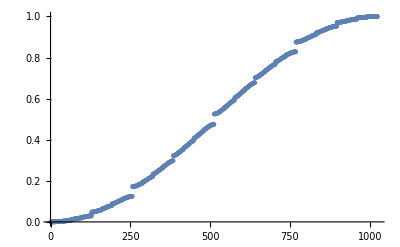

```mathematica
ListPlot@spect[10,.9,1.]
```

Compute Hausdorff dimension by box-counting

```mathematica
(* take a fractal set (represented as an ordered list of points between 0 and 1), return the number of filled boxes *)
Clear[bc];
bc[list_,n_,δ_]:=Block[{curLbl=1,curBS,Δ,b=δ^-n,nboxes=0,len=Length[list],loop},(*Δ:distance btw the left side of the current box and the current pt*)
(*Δ=list[[curLbl]]-curBS;*)
Δ=Mod[list[[curLbl]],b];
curBS=list[[curLbl]]-Δ;
While[curLbl<len,loop=False;
(*while the current pt is in the current box,pass to the pt on its right*)
While[Δ≤b&&curLbl<len,curLbl++;Δ=list[[curLbl]]-curBS;];
(*after the loop the current box has jumped of Floor[Δ/b] units,and one more box has points in it*)curBS+=b Floor[Δ/b];
nboxes++;Δ=list[[curLbl]]-curBS;];
Return[nboxes];]
```

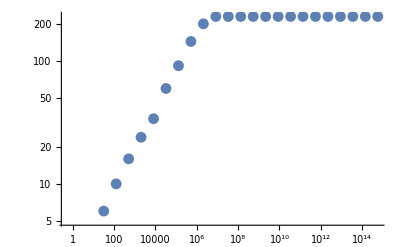

```mathematica
sp=spect[11,.1,1.];
r=Range[5,50,2];
delta=2;
(* compute the number of filled boxes for a whole range of values of n *)
nb=ParallelMap[bc[sp,#,delta]&,r];
(*number of filled boxes as a function of their length*)
dat=Parallelize@MapThread[{#1,#2}&,{delta^r,nb}];
(* the slope is the box-counting dimension of the spectrum *)
ListLogLogPlot[dat]
```

```mathematica
(* now we can fit the slope to get the box-counting dimension *)
xi=4;xf=xi+12;
fit=LinearModelFit[Log10@dat[[xi;;xf]],logl,logl];
Plot[Normal@fit,{logl,0,15},Axes->False,Frame->True,Epilog->{PointSize@.02,Point@Log10@dat},PlotLegends->Placed[Normal@fit,{Right,Center}]]
```

-Graphics-

```mathematica
FractalD[13,.1,1.,0]
```

-0.316947

Compute generalized dimensions by box-counting

```mathematica
(* take a fractal set (represented as an ordered list of points between 0 and 1), return the number of filled boxes *)
Clear[RenyiBc];
RenyiBc[list_,n_,δ_,q_]:=Block[{curLbl=1,curBS=0,Δ,b=δ^-n,qnorm=0,ntot=Length[list],npts=0,len=Length[list],loop},
(*Δ:distance btw the left side of the current box and the current pt*)
Δ=Mod[list[[curLbl]],b];
curBS=list[[curLbl]]-Δ;
While[curLbl≤len,
(* there is for now 0 pt in the current box *)
npts=0;
(*while the current pt is in the current box,pass to the pt on its right*)
While[Δ≤b,
curLbl++;
npts++;
If[curLbl≤ len,Δ=list[[curLbl]]-curBS,Break[]];
];
qnorm+=(npts/ntot)^q;
If[curLbl>len,Break[]];
(*after the loop the current box has jumped of Floor[Δ/b] units*)
curBS+=b Floor[Δ/b];
Δ=list[[curLbl]]-curBS;
];
Return[qnorm];]
```

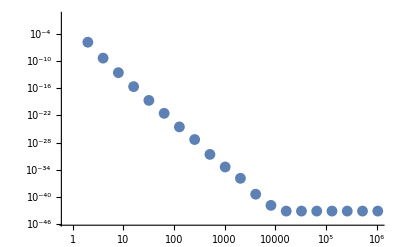

```mathematica
sp=spect[12,1.,1.];
r=Range[1,20,1];
delta=2;
(* compute the number of filled boxes for a whole range of values of n *)
nb=ParallelMap[RenyiBc[sp,#,delta,20]&,r];
(*number of filled boxes as a function of their length*)
dat2=Parallelize@MapThread[{#1,#2}&,{delta^r,nb}];
(* the slope is the box-counting dimension of the spectrum *)
ListLogLogPlot[{dat2}]
```

```mathematica
(* now we can fit the slope to get the box-counting dimension *)
xi=1;xf=xi+10;
fit=LinearModelFit[Log10@dat2[[xi;;xf]],logl,logl];
Plot[Normal@fit,{logl,0,7},Axes->False,Frame->True,Epilog->{PointSize@.02,Point@Log10@dat2},PlotLegends->Placed[Normal@fit,{Right,Center}]]
```

-Graphics-

### Comparison asymptotically exact/numerical solution in the ρ → 0 limit.

#### D_q

```mathematica
Col[l1_,l2_]:=MapThread[{#1,#2}&,{l1,l2}];
```

```mathematica
(* asymptotically exact solution in the ρ->0 limit *)
exactFD[ρ_,q_]:=Block[{ω=1/GoldenRatio,z,barz},
z=ρ/2;
barz=ρ^2;
τ/.FindRoot[2 ω^(2q)z^-τ+ω^(3q)barz^-τ-1,{τ,10}]
]
```

```mathematica
err[q_]:=Block[{i=11,listρ,numd2,exactd2,dat},
(* ρ = Subscript[t, w]/Subscript[t, s] *)
listρ=Table[1.2^-it,{it,1,15}];
(* numerical Rényi entropy for ρ in listρ *)
numd2=ParallelMap[FractalD[i,#,1.,q]&,listρ];
(* asymptotically exact Rényi entropy for ρ in listρ *)
exactd2=exactFD[#,q]&/@listρ;
dat=Col[listρ^-1,Abs[numd2-exactd2]/Abs[q-1]];
(*Print[ListLogLogPlot[dat]];*)
dat
]
```

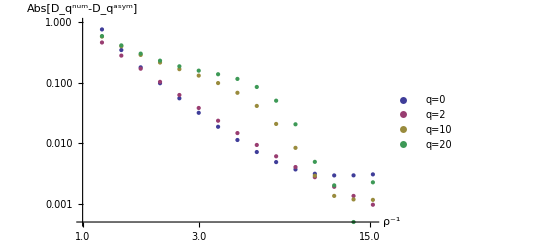

```mathematica
ListLogLogPlot[err[#]&/@#,PlotLegends->("q="<>ToString@#&/@#),AxesLabel->{"ρ^-1",Abs[Subscript[D, q]^num-Subscript[D, q]^asym]}]&@{0,2,10,20}
```

Convergence is good with Γ^(n+2)/Γ^n for q<0, and is good with Γ^(n+1)/Γ^n for q>0.

```mathematica
(* Compute the fractal dimension Subscript[D, q0] for a system of size fib(i+2) *)
Clear[FractalD2];
FractalD2[i_,tw_,ts_,q0_]:=Block[{vpp,vpa,vppN,vpaN,bandlist,bandlistN,gam,gamN,τ0},
(* spectres des systèmes de taille i p et anti-p *)
vpp=Sort[Eigenvalues[hp[i,tw,ts]]];
vpa=Sort[Eigenvalues[ha[i,tw,ts]]];
(* spectres des systèmes de taille i+1 p et anti-p *)
vppN=Sort[Eigenvalues[hp[i+2,tw,ts]]];
vpaN=Sort[Eigenvalues[ha[i+2,tw,ts]]];
(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bandlist=MapThread[Abs[#1-#2]&,{vpa,vpp}];
bandlistN=MapThread[Abs[#1-#2]&,{vpaN,vppN}];
(* calcul des fonctions de partition Subscript[Γ, i] et Subscript[Γ, i+1] *)
gam=Fibonacci[i+2]^-q Plus@@((bandlist)^-τ);
gamN=Fibonacci[i+4]^-q Plus@@((bandlistN)^-τ);
(* Subscript[D, q0] *)
τ0=τ/.FindRoot[(gamN/gam/.q->q0)-1,{τ,0}];
τ0
]
```

```mathematica
err2[q_]:=Block[{i=11,listρ,numd2,exactd2,dat},
(* ρ = Subscript[t, w]/Subscript[t, s] *)
listρ=Table[1.2^-it,{it,1,15}];
(* numerical Rényi entropy for ρ in listρ *)
numd2=ParallelMap[FractalD2[i,#,1.,q]&,listρ];
(* asymptotically exact Rényi entropy for ρ in listρ *)
exactd2=exactFD[#,q]&/@listρ;
dat=Col[listρ^-1,Abs[numd2-exactd2]/Abs[q-1]];
(*Print[ListLogLogPlot[dat]];*)
dat
]
```

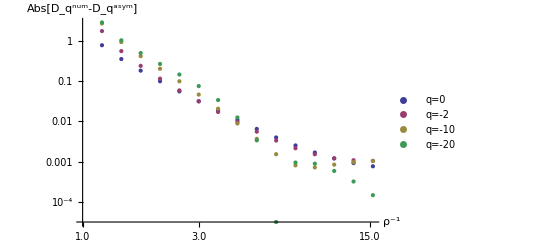

```mathematica
ListLogLogPlot[err2[#]&/@#,PlotLegends->("q="<>ToString@#&/@#),AxesLabel->{"ρ^-1",Abs[Subscript[D, q]^num-Subscript[D, q]^asym]}]&@{0,-2,-10,-20}
```

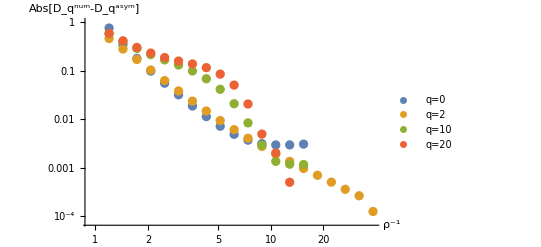

```mathematica
ListLogLogPlot[{errq0,errq2,errq10,errq20},PlotLegends->{"q="<>#&/@{"0","2","10","20"}},AxesLabel->{"ρ^-1",Abs[Subscript[D, q]^num-Subscript[D, q]^asym]}]
Export[dir<>"/data/numerical_vs_asymptotic_FD.pdf",%];
```

#### q→τ(q)

```mathematica
ClearAll[f,alpha];
exactFA[ρ_]:=Block[{z=ρ/2,barz=ρ^2,ω=N[1/GoldenRatio],f,alpha},
alpha=Log[ω]/(x Log[z]+(1-2x)/3 Log[barz]);
f=(x Log[3x/2]-(1+x)Log[(1+x)^(1/3)]+(1-2x)Log[(1-2x)^(1/3)])/(x Log[z]+(1-2x)/3 Log[barz]);
{alpha,f}
]
```

```mathematica
(* asymptotically exact solution in the ρ->0 limit *)
exactFD[ρ_,q_]:=Block[{ω=1/GoldenRatio,z,barz},
z=ρ/2;
barz=ρ^2;
τ/.FindRoot[2 ω^(2q)z^-τ+ω^(3q)barz^-τ-1,{τ,1}]
]
```

```mathematica
(* Return banlists *)
Clear[BandLists];
BandLists[i_,tw_,ts_]:=Block[{vpp,vpa,vppN,vpaN,bandlist,bandlistN},
(* spectres des systèmes de taille i p et anti-p *)
vpp=Sort[Eigenvalues[hp[i,tw,ts]]];
vpa=Sort[Eigenvalues[ha[i,tw,ts]]];
(* spectres des systèmes de taille i+1 p et anti-p *)
vppN=Sort[Eigenvalues[hp[i+2,tw,ts]]];
vpaN=Sort[Eigenvalues[ha[i+2,tw,ts]]];
(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bandlist=MapThread[Abs[#1-#2]&,{vpa,vpp}];
bandlistN=MapThread[Abs[#1-#2]&,{vpaN,vppN}];
{bandlist,bandlistN}
]
(* Return τ -> q *)
Clear[TauQ];
TauQ[τmin_,τmax_,bandlist_,bandlistN_]:=Block[{q,alpha,f,om=N[2/(1+√5)]},
(* q(τ) *)
q=Log[Plus@@((bandlistN)^-τ)/Plus@@((bandlist)^-τ)];
(*q=q/Log[Fibonacci[Length@bandlistN]/Fibonacci[Length@bandlist]];*)
q
]
```

```mathematica
{b,bnew}=BandLists[11,.1,1.];
```

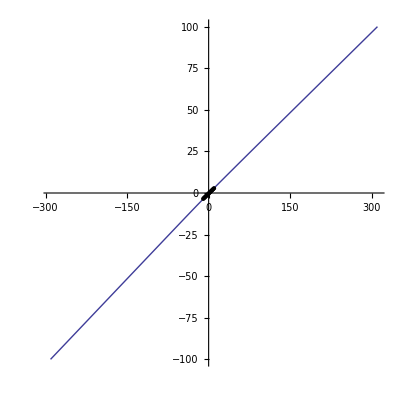

```mathematica
ParametricPlot[{TauQ[-20,20,b,bnew],τ},{τ,-100,100},AspectRatio->1,PlotRange->All,Epilog->Point@Table[{q,exactFD[.1,q]},{q,-10,10}]]
```

```mathematica
(* brute force!!!! *)
ClearAll[th,num];
num=ParallelTable[FractalFa[11,.1,1.,
```